## Using PRIMAT to get abundances on a grid of (Ω_b h^2,N_ν) values. Used to provide a table for CAMB.

### Loading PRIMAT

Setting the notebook directory (in batch mode this is not evaluated because it seems to be the default one)

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we go the parent directory, or base directory of PRIMAT.

```mathematica
SetDirectory[ParentDirectory[Directory[]]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

We load PRIMAT. It takes some time because it starts reading the file with nuclear reactions and deduces which are the nuclides needed, 
and it starts to build formally the network of equations

```mathematica
Timing[<<PRIMAT-Main.m]
```

{22.0907,Null}

### Ad-hoc definitions for Yp, Yp^BBN, η_0.

```mathematica
mbaryonEndBBN[xHe4_]:=((1-xHe4)H1Overma+xHe4/4 He4Overma)ma;
YPMassFraction[xHe4_]:=xHe4/4*He4Overma*ma/mbaryonEndBBN[xHe4];
Ωbh2OverηEndBBN[xHe4_]:=Subscript[n, CMB0]/ρcrit100 mbaryonEndBBN[xHe4]/(clight)^2;
η0EndBBN[Ωbh2_,xHe4_]:=Ωbh2/Ωbh2OverηEndBBN[xHe4];
```

The text to be prepended for the output file

```mathematica
TextPreambule = "# BBN prediction of the primordial abundances (He-4 and Deuterium) as a function of
# 1)the baryon density $\\Omega_b h^2$ and 
# 2)the number of extra relativistic degrees of freedom $\\Delta N$
# 
# If $\\Delta N=0$, then $N_{eff} = 3.045$ because of QED effects and Incomplete Neurino decoupling.
#
# Computation performed with PRIMAT (by Cyril Pitrou 2018 http://www2.iap.fr/users/pitrou/primat.htm)
# Details on arXiv:1801.08023
# Last update 24/03/2018
#
# Neutron Decay rate $\\tau_n$ is 879.5s (+-0.8s), following Serebrov et al. 2017 (arXiv:1712.05663)
# CMB temperature is 2.7255 K (without taking into account a possible uncertainty)
#
# He4 is given either as $Y^BBN_P = 4 Y_{He4}$ where $Y_{He4}$ is the ratio of He-4 number density to baryons number density.
# He4 is also provided as $Y_P = Y_{He4} * m_ {He4} /[Y_{He4} m_{He4} + (1 - 4*Y_{He4}) m_H1]$ 
# where $m_{He4}=4.0026032541$ and $m_{H1}=1.00782503223$ are atomic masses. 
#
# Deuterium is given as the ratio of its number density to the H1 number density and noted $D/H$.
# 
# eta10 is $10^10 eta_0$ where $eta_0$ is the density ratio between baryons and photons AT THE END OF BBN.
# Hence eta10 ignores the extra production of He4 by stars after BBN. Whenever possible, working with $\\Omega_b h^2$ is better. 
#
# Errors are computed with a Monte-Carlo method on nuclear rates and also on tau_n. 
# See PRIMAT paper (2018) for details.
# 
#  Ombh2        eta10           DeltaN          Yp              Yp^BBN          sig(Yp^BBN)     D/H             sig(D/H)  \n";
```

### Set - up

Choice of number of points for the Monte - Carlo to estimate errors

```mathematica
$ComputeErrors=True;
$NPointsMC=20;
```

Some options to parallelize

```mathematica
$ParallelBool2D=True;
$ParallelBool=False;
```

No neutrino degeneracy. No radnom on baryons because we shall compute on a grid of baryon abundance

```mathematica
$DegenerateNeutrinos=False;
$Randomh2Ωb=False;
```

We reset some parameters (useless)

```mathematica
Meanh2Ωb0=h2Ωb0;
μOverTν=0;
NeutrinosGenerations=3;
```

Custom Parallelization

```mathematica
MyMap2D:=If[$ParallelBool2D,
InitializeKernels;
ParallelEvaluate[$HistoryLength=0;];
ParallelMap,
Map]
```

Rounding function for exporting results (To avoid 15 digits...)

```mathematica
NF6[num_]:=NumberForm[num,{6,6}];
MyFortranForm[num_]:=SetPrecision[num,6];
```

Table of N_ν, Ω_b h^2

```mathematica
Listω=DeleteDuplicates@Join[Table[ω,{ω,0.005,0.02,0.001}],Table[ω,{ω,0.02,0.024,0.0002}],Table[ω,{ω,0.024,0.04,0.001}]];
ListdN=DeleteDuplicates@Join[Table[dΝ,{dΝ,-3,-1,.5}],Table[dΝ,{dΝ,-1,1,0.25}],Table[dΝ,{dΝ,1,7,.5}]];
```

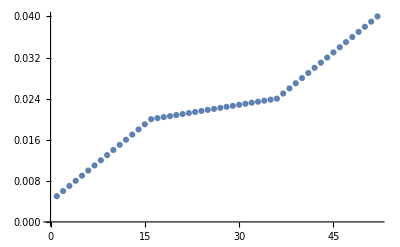

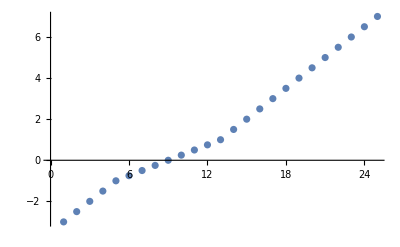

```mathematica
ListPlot@Listω
ListPlot@ListdN
```

```mathematica
TabledNω=Table[{dΝν,ω},{dΝν,ListdN},{ω,Listω}];
(*TabledNω=Table[{dΝν,ω},{dΝν,0.,0.,1},{ω,0.02225,0.02225,0.001}];*)
```

```mathematica
TabledNω//Dimensions
```

{25,52,2}

```mathematica
ComputePrincipalAbundancedNω[{dNν_,ω_}]:=Module[{σXP,σDH,XP,DH,XPList,DHList,ResultMean,Resultσ,Meanh2Ωb0Old,NeutrinosGenerationsOld},
NeutrinosGenerationsOld=NeutrinosGenerations;
Meanh2Ωb0Old=Meanh2Ωb0;
Meanh2Ωb0=ω;
NeutrinosGenerations=3+dNν;

(* Run first without MonteCarlo amd good precision *)
Print["Dealing With ",ω," ",dNν];
$RandomNuclearRates=False;
$Randomτneutron=False;
PrecisionNDSolve=2;
RunPRIMAT;

XPList=4ElementColumn["a"];
DHList=(*10^5*)ElementColumn["d"]/ElementColumn["p"];
XP=Mean[XPList];
DH=Mean[DHList];

(* Then run with MonteCarlo and poor precision *)
If[$ComputeErrors,
PrecisionNDSolve=0;
$RandomNuclearRates=True;
$Randomτneutron=True;
RunPRIMATMonteCarlo[$NPointsMC];
XPList=4ElementColumn["a"];
DHList=(*10^5*)ElementColumn["d"]/ElementColumn["p"];
σXP=StandardDeviation[XPList];
σDH=StandardDeviation[DHList];,
σXP=0.000;
σDH=0.000;
];

NeutrinosGenerations=NeutrinosGenerationsOld;
Meanh2Ωb0=Meanh2Ωb0Old;
Print[ω," ",dNν,"  ",XP," ",σXP," ",DH," ",σDH," "];
{NF6@ω,NF6[10^10. η0EndBBN[ω,XP]],NF6[dNν],NF6[YPMassFraction[XP]],NF6[XP],MyFortranForm[σXP],MyFortranForm[DH],MyFortranForm[σDH]}
]
```

### Actual computation and export of results for CAMB (Takes many many hours, if not days...)

```mathematica
Timing[TableForCAMB=MyMap2D[ComputePrincipalAbundancedNω,TabledNω,{2}];];
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

Number of Kernels 2

Dealing With 0.02225 0.

Iteration 1  Memory usage = 61198808 time = 74.5474  Kernel : 2

Running a Monte-Carlo with 12 points.

Iteration 1  Memory usage = 54757984 time = 30.1498  Kernel : 2

Iteration 2  Memory usage = 54591984 time = 30.5579  Kernel : 2

Iteration 3  Memory usage = 54571328 time = 30.7357  Kernel : 2

Iteration 4  Memory usage = 54687304 time = 30.466  Kernel : 2

Iteration 5  Memory usage = 54713488 time = 31.8292  Kernel : 2

Iteration 6  Memory usage = 54811072 time = 30.7857  Kernel : 2

Iteration 7  Memory usage = 54639816 time = 30.2487  Kernel : 2

Iteration 8  Memory usage = 54759776 time = 30.5396  Kernel : 2

Iteration 9  Memory usage = 54749552 time = 32.2806  Kernel : 2

Iteration 10  Memory usage = 54663176 time = 29.6117  Kernel : 2

Iteration 11  Memory usage = 54805496 time = 32.4804  Kernel : 2

Iteration 12  Memory usage = 54913016 time = 29.7827  Kernel : 2

0.02225 0.  0.247093 0.000303509 0.0000245919 3.00453×10^-7

```mathematica
Export["MonteCarlo/PRIMAT_Yp_DH_ErrorMC"<>ToString[$NPointsMC]<>".dat",Prepend[Flatten[TableForCAMB,1],TextPreambule],"TSV"]
```